```mathematica
Clear[sol,x]
sol=DSolve[{x''[t]+x[t]^3==0,x[0]==1,x'[0]==0},x[t],{t,0,10}]
```

{{x[t]→JacobiCD[t/(√2),-1]}}

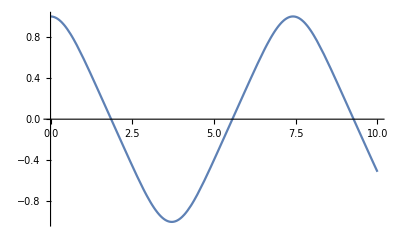

```mathematica
Plot[Evaluate[x[t]/.sol],{t,0,10}]
```

```mathematica
Integrate[4(2m/k)^(1/2)/(A^4-x^4)^(1/2),{x,0,A}]
```

```mathematica
4 ⅈ √2 (1/A)^(5/2) √(-A^3) √(m/k) EllipticF[(ⅈ √(-1/A) π)/(2 √(1/A)),-1]
```

4 ⅈ √2 (1/A)^(5/2) √(-A^3) √(m/k) EllipticF[(ⅈ √(-1/A) π)/(2 √(1/A)),-1]

```mathematica
%*(-A^3)^(1/2)
```

-(4 ⅈ √2 √(m/k) EllipticF[(ⅈ √(-1/A) π)/(2 √(1/A)),-1])/(√(1/A))

```mathematica
%/I*A(3/2)
```

-(6 √2 √(m/k) EllipticF[(ⅈ √(-1/A) π)/(2 √(1/A)),-1])/(1/A)^(3/2)

```mathematica
FullSimplify[%]
```

-(6 √2 √(m/k) EllipticF[(ⅈ √(-1/A) π)/(2 √(1/A)),-1])/(1/A)^(3/2)